# Proggetto Automatica-Traccia 29 Luca Timpano 240236

```mathematica
ClearAll["Global *"]
```

## Tempo Discreto

### Dati

```mathematica
A = {{28/75,-113/150,2/5},{-19/75,37/75,-1/5},{-47/75,37/150,-3/5}}
```

{{28/75,-113/150,2/5},{-19/75,37/75,-1/5},{-47/75,37/150,-3/5}}

```mathematica
B = {{1/2},{1},{1/2}}
```

{{1/2},{1},{1/2}}

```mathematica
C1 = {{9/8,-1,7/8}}
```

{{9/8,-1,7/8}}

```mathematica
A // MatrixForm
```

(28/75 | -113/150 | 2/5
-19/75 | 37/75 | -1/5
-47/75 | 37/150 | -3/5)

```mathematica
B // MatrixForm
```

(1/2
1
1/2)

```mathematica
C1 // MatrixForm
```

(9/8 | -1 | 7/8)

### Modi Naturali

#### Autovalori

```mathematica
λ=Eigenvalues[A]
```

{2/3,-1/5,-1/5}

#### Molteplicità geometrica

```mathematica
NullSpace[A-(2/3)IdentityMatrix[3]]
```

{{-11/7,8/7,1}}

```mathematica
NullSpace[A-(-1/5)IdentityMatrix[3]]
```

{{-19/31,2/31,1}}

#### Matrice di Jordan

```mathematica
{T,Λ}  = JordanDecomposition[A]
```

{{{-19/31,-1750/961,-11/7},{2/31,-550/961,8/7},{1,0,1}},{{-1/5,1,0},{0,-1/5,0},{0,0,2/3}}}

```mathematica
T // MatrixForm
```

(-19/31 | -1750/961 | -11/7
2/31 | -550/961 | 8/7
1 | 0 | 1)

```mathematica
Λ // MatrixForm
```

(-1/5 | 1 | 0
0 | -1/5 | 0
0 | 0 | 2/3)

#### Modi Naturali

```mathematica
MatrixPower[Λ ,k] // MatrixForm
```

((-1/5)^k | -(-1)^k 5^(1-k) k | 0
0 | (-1/5)^k | 0
0 | 0 | (3/2)^-k)

```mathematica
M = {(-1/5)^k,-(-1)^k 5^(1-k) k,(3/2)^-k}
```

{(-1/5)^k,-(-1)^k 5^(1-k) k,(3/2)^-k}

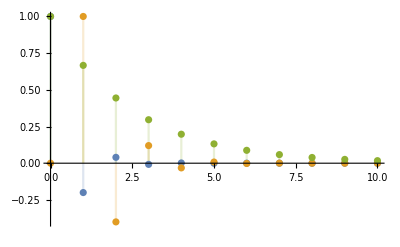

```mathematica
DiscretePlot[{(-1/5)^k,-(-1)^k 5^(1-k) k,(3/2)^-k},{k,0,10},PlotRange->All]
```

### Risposta libera

```mathematica
Subscript[x, 0] = {{1},{2},{-3}}
```

{{1},{2},{-3}}

```mathematica
Subscript[y, l][k_]:= Expand[Simplify[MatrixPower[A ,k].Subscript[x, 0]]]
```

```mathematica
Subscript[y, l][k]
```

{{-473/169 (2/3)^k+642/169 5^-k ⅇ^(ⅈ k π)-19/13 5^-k ⅇ^(ⅈ k π) k},{43/169 2^(3+k) 3^-k-6/169 5^-k ⅇ^(ⅈ k π)+2/13 5^-k ⅇ^(ⅈ k π) k},{301/169 (2/3)^k-808/169 5^-k ⅇ^(ⅈ k π)+31/13 5^-k ⅇ^(ⅈ k π) k}}

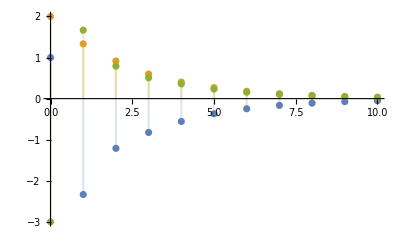

```mathematica
DiscretePlot[{{-473/169 (2/3)^k+642/169 5^-k ⅇ^(ⅈ k π)-19/13 5^-k ⅇ^(ⅈ k π) k},{43/169 2^(3+k) 3^-k-6/169 5^-k ⅇ^(ⅈ k π)+2/13 5^-k ⅇ^(ⅈ k π) k},{301/169 (2/3)^k-808/169 5^-k ⅇ^(ⅈ k π)+31/13 5^-k ⅇ^(ⅈ k π) k}},{k,0,10},PlotRange->All]
```

#### Traformata Z

```mathematica
Subscript[y, lz][k_]:= z Inverse[z IdentityMatrix[3]-A].Subscript[x, 0]
```

```mathematica
MatrixForm[Expand[Simplify[Subscript[y, lz][k]]]]
```

(-(61 z)/((-2+3 z) (1+5 z)^2)-(195 z^2)/((-2+3 z) (1+5 z)^2)+(75 z^3)/((-2+3 z) (1+5 z)^2)
(8 z)/((-2+3 z) (1+5 z)^2)+(60 z^2)/((-2+3 z) (1+5 z)^2)+(150 z^3)/((-2+3 z) (1+5 z)^2)
(77 z)/((-2+3 z) (1+5 z)^2)+(185 z^2)/((-2+3 z) (1+5 z)^2)-(225 z^3)/((-2+3 z) (1+5 z)^2))

```mathematica
MatrixForm[Expand[InverseZTransform[Subscript[y, lz][k],z,k]]]
```

(642/169 (-1/5)^k-473/169 (2/3)^k-19/13 (-1/5)^k k
-6/169 (-1/5)^k+43/169 2^(3+k) 3^-k+2/13 (-1/5)^k k
-808/169 (-1/5)^k+301/169 (2/3)^k+31/13 (-1/5)^k k)

```mathematica
DiscretePlot[{{{642/169 (-1/5)^k-473/169 (2/3)^k-19/13 (-1/5)^k k}, {-6/169 (-1/5)^k+43/169 2^(3+k) 3^-k+2/13 (-1/5)^k k}, {-808/169 (-1/5)^k+301/169 (2/3)^k+31/13 (-1/5)^k k}}},{k,0,10},PlotRange->All]
```

-Graphics-

### Configurazione stati inziali

```mathematica
T // MatrixForm
```

(-19/31 | -1750/961 | -11/7
2/31 | -550/961 | 8/7
1 | 0 | 1)

```mathematica
x1 = 5*Transpose[T][[1]]
```

{-95/31,10/31,5}

```mathematica
Subscript[x, l1] [k_]:=Simplify[MatrixPower[A ,k].x1]
```

```mathematica
Subscript[x, l1] [k] // MatrixForm
```

(-19/31 5^(1-k) ⅇ^(ⅈ k π)
2/31 5^(1-k) ⅇ^(ⅈ k π)
5^(1-k) ⅇ^(ⅈ k π))

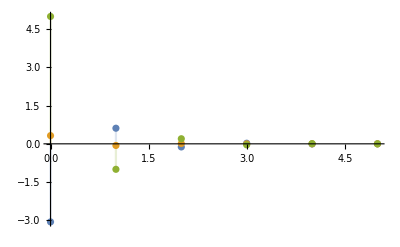

```mathematica
DiscretePlot[{({{-19/31 5^(1-k) ⅇ^(ⅈ k π)}, {2/31 5^(1-k) ⅇ^(ⅈ k π)}, {5^(1-k) ⅇ^(ⅈ k π)}})},{k,0,5},PlotRange->All]
```

```mathematica
x2 = 5*Transpose[T][[1]] + 5*Transpose[T][[2]]
```

{-11695/961,-2440/961,5}

```mathematica
Subscript[x, l2] [k_]:=Simplify[MatrixPower[A ,k].x2]
```

```mathematica
Subscript[x, l2] [k] // MatrixForm
```

(1/961 5^(1-k) ⅇ^(ⅈ k π) (-2339+2945 k)
-2/961 5^(1-k) ⅇ^(ⅈ k π) (244+155 k)
5^(1-k) ⅇ^(ⅈ k π) (1-5 k))

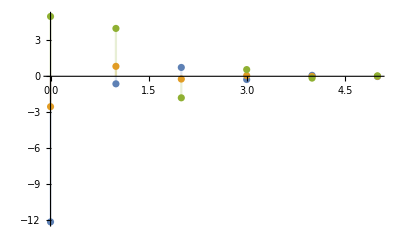

```mathematica
DiscretePlot[{{{1/961 5^(1-k) ⅇ^(ⅈ k π) (-2339+2945 k)}, {-2/961 5^(1-k) ⅇ^(ⅈ k π) (244+155 k)}, {5^(1-k) ⅇ^(ⅈ k π) (1-5 k)}}},{k,0,5},PlotRange->All]
```

### Funzione di trasferimento

```mathematica
G[z_]:=Simplify[C1.Inverse[z IdentityMatrix[3]-A].B][[1,1]]
```

```mathematica
G[z]
```

-(75 (1+8 z))/(8 (-2+3 z) (1+5 z)^2)

#### Zeri

```mathematica
Solve[Numerator[G[z]]== 0,z]
```

{{z→-1/8}}

#### Poli

```mathematica
Solve[Denominator[G[z]]== 0,z]
```

{{z→-1/5},{z→-1/5},{z→2/3}}

### Risposta al Gradino Unitario

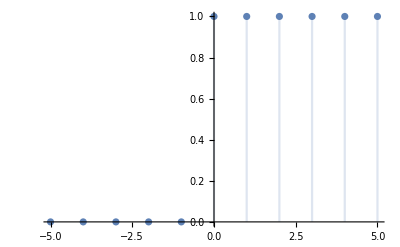

```mathematica
DiscretePlot[{UnitStep[k]},{k,-5,5}, PlotRange->All]
```

```mathematica
U[z_]:= ZTransform[UnitStep[k],k,z]
```

```mathematica
U[z]
```

z/(-1+z)

```mathematica
Subscript[Y, f][z_]:= G[z]*U[z]
```

```mathematica
Subscript[Y, f][z]
```

-(75 z (1+8 z))/(8 (-1+z) (-2+3 z) (1+5 z)^2)

```mathematica
Subscript[y, f][k] = Expand[Simplify[ComplexExpand[InverseZTransform[Subscript[Y, f][z],z,k]]]]
```

-75/32+475/169 2^(-3+k) 3^(2-k)-(177 5^(2-k) Cos[k π])/5408-3/208 5^(2-k) k Cos[k π]-(177 ⅈ 5^(2-k) Sin[k π])/5408-3/208 ⅈ 5^(2-k) k Sin[k π]

#### Risposta a regime

```mathematica
Subscript[y, freg][k] = lim _(k->+∞) Subscript[y, f][k]
```

-75/32

#### Risposta transitoria

```mathematica
Subscript[y, ftrans][k]= 475/169 2^(-3+k) 3^(2-k)-(177 5^(2-k) Cos[k π])/5408-3/208 5^(2-k) k Cos[k π]-(177 ⅈ 5^(2-k) Sin[k π])/5408-3/208 ⅈ 5^(2-k) k Sin[k π]
```

475/169 2^(-3+k) 3^(2-k)-(177 5^(2-k) Cos[k π])/5408-3/208 5^(2-k) k Cos[k π]-(177 ⅈ 5^(2-k) Sin[k π])/5408-3/208 ⅈ 5^(2-k) k Sin[k π]

#### Grafico

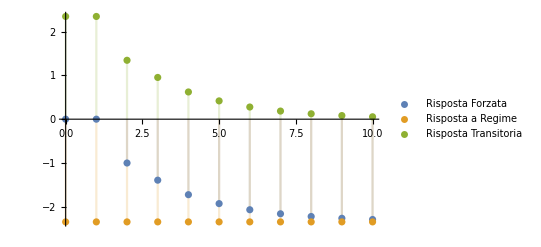

```mathematica
DiscretePlot[{{-75/32+475/169 2^(-3+k) 3^(2-k)-(177 5^(2-k) Cos[k π])/5408-3/208 5^(2-k) k Cos[k π]-(177 ⅈ 5^(2-k) Sin[k π])/5408-3/208 ⅈ 5^(2-k) k Sin[k π]},{-75/32},{475/169 2^(-3+k) 3^(2-k)-(177 5^(2-k) Cos[k π])/5408-3/208 5^(2-k) k Cos[k π]-(177 ⅈ 5^(2-k) Sin[k π])/5408-3/208 ⅈ 5^(2-k) k Sin[k π]}},{k,0,10}, PlotRange->All,PlotLegends->{"Risposta Forzata","Risposta a Regime","Risposta Transitoria"}]
```

### Modelli ARMA

```mathematica
Subscript[G, armaz][z_] := Expand[Numerator[G[z]]]/Expand[Denominator[G[z]]]
```

```mathematica
Subscript[G, armaz][z]
```

(-75-600 z)/(-16-136 z-160 z^2+600 z^3)

```mathematica
ARMAZ =Expand[Denominator[Subscript[G, armaz][z]] Y[z]==Numerator[Subscript[G, armaz][z]] Subscript[U, 1][z]]
```

-16 Y[z]-136 z Y[z]-160 z^2 Y[z]+600 z^3 Y[z]==-75 U_1[z]-600 z U_1[z]

```mathematica
Subscript[ARMA, ant] = ARMAZ /. {Y[z]->y[k], z Y[z]-> y[k+1],  z^2 Y[z]->y[k+2], z^3 Y[z]->y[k+3], Subscript[U, 1][z]->u[k], z Subscript[U, 1][z]->u[k+1] }
```

-16 y[k]-136 y[1+k]-160 y[2+k]+600 y[3+k]==-75 u[k]-600 u[1+k]

```mathematica
Subscript[ARMA, rit]= ARMAZ /. {Y[z]->y[k'-3], z Y[z]-> y[k'-2],  z^2 Y[z]->y[k'-1], z^3 Y[z]->y[k'], Subscript[U, 1][z]->u[k'-3], z Subscript[U, 1][z]->u[k'-2] }
```

-16 y[-3+k']-136 y[-2+k']-160 y[-1+k']+600 y[k']==-75 u[-3+k']-600 u[-2+k']

#### Condizioni inziali

```mathematica
Subscript[x, 01] = {{-2},{-2},{3}}
```

{{-2},{-2},{3}}

```mathematica
y0 = (C1[[1]].Subscript[x, 01])[[1]]
```

19/8

```mathematica
y1 = (C1[[1]].A.Subscript[x, 01])[[1]]
```

19/8

```mathematica
y2 = (C1[[1]].A.A.Subscript[x, 01])[[1]]
```

133/100

```mathematica
eqDiffL=Simplify[ZTransform[Subscript[ARMA, ant],k, z]/.{ZTransform[y[k],k,z]->Y[z],ZTransform[u[k],k,z]->Subscript[U, 1][z],u[0]->0}]
```

8 z ((-17-20 z+75 z^2) y[0]+5 (-4+15 z) y[1]+75 y[2])==8 (-2+3 z) (1+5 z)^2 Y[z]+75 (1+8 z) U_1[z]

```mathematica
Ydif[z_]:=Collect[Solve[eqDiffL,Y[z]][[1,1]][[2]], Subscript[U, 1][z]]
```

```mathematica
Ydif[z]
```

(-136 z y[0]-160 z^2 y[0]+600 z^3 y[0]-160 z y[1]+600 z^2 y[1]+600 z y[2])/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) U_1[z])/(8 (-2+3 z) (1+5 z)^2)

```mathematica
Ydif2[z_]:=((-136 z y[0]-160 z^2 y[0]+600 z^3 y[0]-160 z y[1]+600 z^2 y[1]+600 z y[2])/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) Subscript[U, 1][z])/(8 (-2+3 z) (1+5 z)^2))/.{{y[0]-> y0,y[1]->y1,y[2]->y2}}
```

```mathematica
Ydif2[z]
```

{(95 z+1045 z^2+1425 z^3)/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) U_1[z])/(8 (-2+3 z) (1+5 z)^2)}

```mathematica
segnale[k_]:=Piecewise[{{1,0<=k<=10},{0,k>10},{0,k<0}}]
segnale[k]
```

Piecewise[{{1, 0≤k≤10}, {0, True}}]

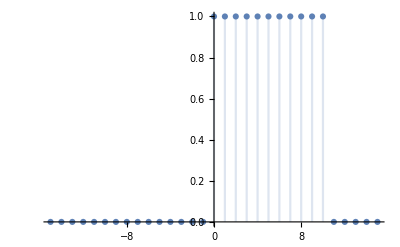

```mathematica
DiscretePlot[{segnale[k]},{k,-15,15}, PlotRange->All]
```

```mathematica
segnalez[z_]:= ZTransform[segnale[k],k,z]
```

```mathematica
segnalez[z]
```

(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)/z^10

```mathematica
Subscript[Y, seg][z_]:= Ydif2[z]/.{{Subscript[U, 1][z]->segnalez[z]}}
```

```mathematica
Subscript[Y, seg][z]
```

{{(95 z+1045 z^2+1425 z^3)/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) (1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10))/(8 z^10 (-2+3 z) (1+5 z)^2)}}

```mathematica
Subscript[Y, segk][k_]:= InverseZTransform[Ydif[z]/.{Subscript[U, 1][z]->segnalez[z], y[0]-> y0,y[1]->y1,y[2]->y2},z,k]
```

```mathematica
Subscript[Y, segk][k]
```

-(3^-k (-425624995555328 (-3/5)^k+739793025 2^k+16250000838656 (-1/5)^k 3^(1+k) k) (1-UnitStep[10-k]))/2768896-(572571261953 UnitStep[10-k] UnitStep[-10+k])/256289062500-(74468859091 UnitStep[9-k] UnitStep[-9+k])/34171875000-(4777277047 UnitStep[8-k] UnitStep[-8+k])/2278125000-(37466066 UnitStep[7-k] UnitStep[-7+k])/18984375-(905687 UnitStep[6-k] UnitStep[-6+k])/506250-(1018573 UnitStep[5-k] UnitStep[-5+k])/675000-(49633 UnitStep[4-k] UnitStep[-4+k])/45000-(653 UnitStep[3-k] UnitStep[-3+k])/1500+33/100 UnitStep[2-k] UnitStep[-2+k]+19/8 (UnitStep[1-k] UnitStep[-1+k]+UnitStep[-k] UnitStep[k]-UnitStep[1-k] UnitStep[-1+k] UnitStep[-k] UnitStep[k])

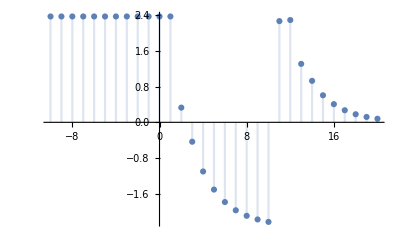

```mathematica
DiscretePlot[1/2768896 3^-k (-425624995555328 (-3/5)^k+739793025 2^k+16250000838656 (-1/5)^k 3^(1+k) k) (1-UnitStep[10-k])-(572571261953 UnitStep[10-k] UnitStep[-10+k])/256289062500-(74468859091 UnitStep[9-k] UnitStep[-9+k])/34171875000-(4777277047 UnitStep[8-k] UnitStep[-8+k])/2278125000-(37466066 UnitStep[7-k] UnitStep[-7+k])/18984375-(905687 UnitStep[6-k] UnitStep[-6+k])/506250-(1018573 UnitStep[5-k] UnitStep[-5+k])/675000-(49633 UnitStep[4-k] UnitStep[-4+k])/45000-(653 UnitStep[3-k] UnitStep[-3+k])/1500+19/8 (1-UnitStep[-2+k])+33/100 UnitStep[2-k] UnitStep[-2+k],{k,-10,20},PlotRange->All]
```

### Stato

```mathematica
Subscript[x, 02] = {{Subscript[x, 11]},{Subscript[x, 22]},{Subscript[x, 33]}}
```

{{x_11},{x_22},{x_33}}

```mathematica
y02 = (C1[[1]].Subscript[x, 02])[[1]]
```

(9 x_11)/8-x_22+(7 x_33)/8

```mathematica
y12 = (C1[[1]].A.Subscript[x, 02])[[1]]
```

x_11/8-(9 x_22)/8+x_33/8

```mathematica
y22 = (C1[[1]].A.A.Subscript[x, 02])[[1]]
```

(19 x_11)/75-(371 x_22)/600+x_33/5

```mathematica
Subscript[ARMA, ant]
```

-16 y[k]-136 y[1+k]-160 y[2+k]+600 y[3+k]==-75 u[k]-600 u[1+k]

```mathematica
eqDiffL2=Simplify[ZTransform[Subscript[ARMA, ant],k, z]/.{ZTransform[y[k],k,z]->Y[z],ZTransform[u[k],k,z]->Subscript[U, 1][z],u[0]->0}]
```

8 z ((-17-20 z+75 z^2) y[0]+5 (-4+15 z) y[1]+75 y[2])==8 (-2+3 z) (1+5 z)^2 Y[z]+75 (1+8 z) U_1[z]

```mathematica
Ydif2[z_]:=Collect[Solve[eqDiffL,Y[z]][[1,1]][[2]], Subscript[U, 1][z]]
```

```mathematica
Ydif2[z]
```

(-136 z y[0]-160 z^2 y[0]+600 z^3 y[0]-160 z y[1]+600 z^2 y[1]+600 z y[2])/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) U_1[z])/(8 (-2+3 z) (1+5 z)^2)

```mathematica
Ydif3[z_]:=((-136 z y[0]-160 z^2 y[0]+600 z^3 y[0]-160 z y[1]+600 z^2 y[1]+600 z y[2])/(8 (-2+3 z) (1+5 z)^2)+((-75-600 z) Subscript[U, 1][z])/(8 (-2+3 z) (1+5 z)^2))/.{{y[0]-> y02,y[1]->y12,y[2]->y22}}
```

```mathematica
Ydif3[z]
```

{1/(8 (-2+3 z) (1+5 z)^2)(-160 z (x_11/8-(9 x_22)/8+x_33/8)+600 z^2 (x_11/8-(9 x_22)/8+x_33/8)+600 z ((19 x_11)/75-(371 x_22)/600+x_33/5)-136 z ((9 x_11)/8-x_22+(7 x_33)/8)-160 z^2 ((9 x_11)/8-x_22+(7 x_33)/8)+600 z^3 ((9 x_11)/8-x_22+(7 x_33)/8))+((-75-600 z) U_1[z])/(8 (-2+3 z) (1+5 z)^2)}

```mathematica
Subscript[Y2, seg][k_]:= Expand[InverseZTransform[Ydif3[z]/.{{Subscript[U, 1][z]->z/(-1+z)}},z,k]]
```

```mathematica
Subscript[Y2, seg][k][[1,1]]
```

-75/32+475/169 2^(-3+k) 3^(2-k)-(177 (-1)^k 5^(2-k))/5408-3/208 (-1)^k 5^(2-k) k+447/676 (-1/5)^k x_11+209/169 2^(-3+k) 3^(1-k) x_11+27/104 (-1/5)^k k x_11+(643 (-1/5)^k x_22)/1352-665/169 2^(-3+k) 3^(1-k) x_22+3/13 (-1/5)^k k x_22+19/169 (3/2)^(3-k) x_33+67/676 (-1)^k 5^(1-k) x_33+3/104 (-1)^k 5^(1-k) k x_33

```mathematica
Yforz[k_] := Expand[InverseZTransform[((-75-600 z) Subscript[U, 1][z])/(8 (-2+3 z) (1+5 z)^2) /.{{Subscript[U, 1][z]->z/(-1+z)}},z,k]]
```

Forzata

```mathematica
Yforz[k]
```

{-75/32+475/169 2^(-3+k) 3^(2-k)-(177 (-1)^k 5^(2-k))/5408-3/208 (-1)^k 5^(2-k) k}

Regime

```mathematica
Yreg[k] := -75/32
```

Transitoria

```mathematica
Ytrans[k] := 475/169 2^(-3+k) 3^(2-k)-(177 (-1)^k 5^(2-k))/5408-3/208 (-1)^k 5^(2-k) k
```

Libera

```mathematica
Ylibz[z_] := ((-136 z y[0]-160 z^2 y[0]+600 z^3 y[0]-160 z y[1]+600 z^2 y[1]+600 z y[2])/(8 (-2+3 z) (1+5 z)^2))/.{{y[0]-> y02,y[1]->y12,y[2]->y22}}
```

```mathematica
Ylibz[z]
```

{1/(8 (-2+3 z) (1+5 z)^2)(-160 z (x_11/8-(9 x_22)/8+x_33/8)+600 z^2 (x_11/8-(9 x_22)/8+x_33/8)+600 z ((19 x_11)/75-(371 x_22)/600+x_33/5)-136 z ((9 x_11)/8-x_22+(7 x_33)/8)-160 z^2 ((9 x_11)/8-x_22+(7 x_33)/8)+600 z^3 ((9 x_11)/8-x_22+(7 x_33)/8))}

Calcolo la transitoria e il regime in z

```mathematica
Ytransz[z_]:= ZTransform[475/169 2^(-3+k) 3^(2-k)-(177 (-1)^k 5^(2-k))/5408-3/208 (-1)^k 5^(2-k) k,k,z]
```

```mathematica
Ytransz[z]
```

(75 z (6+55 z+75 z^2))/(32 (-2+3 z) (1+5 z)^2)

```mathematica
Yregz[z_]:= ZTransform[-75/32,k,z]
```

```mathematica
Yregz[z]
```

-(75 z)/(32 (-1+z))

```mathematica
Numerator[Simplify[Expand[Ylibz[z]+Ytransz[z]]]][[1]]
```

z (450+4125 z+5625 z^2+12 (-7-35 z+225 z^2) x_11-20 (11+103 z+120 z^2) x_22-76 x_33-260 z x_33+2100 z^2 x_33)

```mathematica
aa = CoefficientList[Numerator[Simplify[Expand[Ylibz[z]+Ytransz[z]]]][[1]],z]
```

{0,450-84 x_11-220 x_22-76 x_33,4125-420 x_11-2060 x_22-260 x_33,5625+2700 x_11-2400 x_22+2100 x_33}

```mathematica
Solve[aa=={0,0,0,0},{Subscript[x, 11],Subscript[x, 22],Subscript[x, 33]}]
```

{{x_11→-25/24,x_22→25/12,x_33→25/24}}

```mathematica
x00 = {{-25/24},{25/12},{25/24}}
```

{{-25/24},{25/12},{25/24}}

```mathematica
y002 = (C1[[1]].x00)[[1]]
```

-75/32

```mathematica
y112 = (C1[[1]].A.x00)[[1]]
```

-75/32

```mathematica
y222 = (C1[[1]].A.A.x00)[[1]]
```

-43/32

```mathematica
Ytest[k_]:= Expand[InverseZTransform[Ydif2[z_]/.{Subscript[U, 1][z]->z/(-1+z),y[0]->y002,y[1]->y112,y[2]->y222},z,k]]
```

```mathematica
Ytest[k]
```

-75/32